```mathematica
log={{"(On the carpet) 23:6",{{"23:6",0,0,5,6990},{"23:6",10,0,2,3011},{"23:7",20,0,2,3011},{"23:7",30,0,2,3011},{"23:7",40,0,2,3011},{"23:8",50,0,2,3011},{"23:8",60,0,4,6021},{"23:8",70,0,4,6021},{"23:9",80,0,4,6021},{"23:9",90,0,4,6021},{"23:9",100,0,4,6021},{"23:10",0,1,84,19243},{"23:10",10,1,36,15564},{"23:10",20,1,36,15564},{"23:11",30,1,36,15564},{"23:11",40,1,36,15564},{"23:11",50,1,58,17635},{"23:12",60,1,58,17635},{"23:12",70,1,58,17635},{"23:12",80,1,58,17635},{"23:13",90,1,58,17635},{"23:13",100,1,92,19638}}},{"(On the table) 23:17",{{"23:17",0,0,5,6990},{"23:17",10,0,4,6021},{"23:18",20,0,4,6021},{"23:18",30,0,4,6021},{"23:18",40,0,4,6021},{"23:19",50,0,4,6021},{"23:19",60,0,4,6021},{"23:19",70,0,4,6021},{"23:20",80,0,4,6021},{"23:20",90,0,4,6021},{"23:20",100,0,4,6021},{"23:21",0,1,44,16435},{"23:21",10,1,19,12788},{"23:21",20,1,19,12788},{"23:22",30,1,19,12788},{"23:22",40,1,19,12788},{"23:22",50,1,32,15052},{"23:23",60,1,32,15052},{"23:23",70,1,32,15052},{"23:23",80,1,32,15052},{"23:24",90,1,32,15052},{"23:24",100,1,32,15052}}},{"(Under the lamp) 23:26",{{"23:26",0,0,9,9543},{"23:26",10,0,4,6021},{"23:27",20,0,4,6021},{"23:27",30,0,4,6021},{"23:27",40,0,4,6021},{"23:28",50,0,4,6021},{"23:28",60,0,7,8451},{"23:28",70,0,7,8451},{"23:29",80,0,7,8451},{"23:29",90,0,7,8451},{"23:29",100,0,7,8451},{"23:30",0,1,116,20645},{"23:30",10,1,73,18634},{"23:30",20,1,73,18634},{"23:31",30,1,73,18634},{"23:31",40,1,117,20682},{"23:31",50,1,117,20682},{"23:32",60,1,117,20682},{"23:32",70,1,117,20682},{"23:32",80,1,117,20682},{"23:33",90,1,196,22923},{"23:33",100,1,196,22923}}}};
```

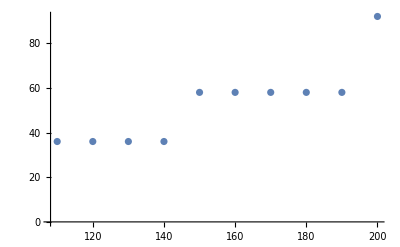

```mathematica
log2=Table[
{log[[i,2,s,2]]+100*log[[i,2,s,3]],
log[[i,2,s,3+k]]}
,{k,2},{i,Length@log},{s,Length@log[[i,2]]}];
log3=log2[[1,1,13;;22]];
ListPlot[log3]
```

-25.7455+0.505455 x

76.1939-0.856667 x+0.00439394 x^2

-325.924+7.26321 x-0.0490793 x^2+0.000114996 x^3

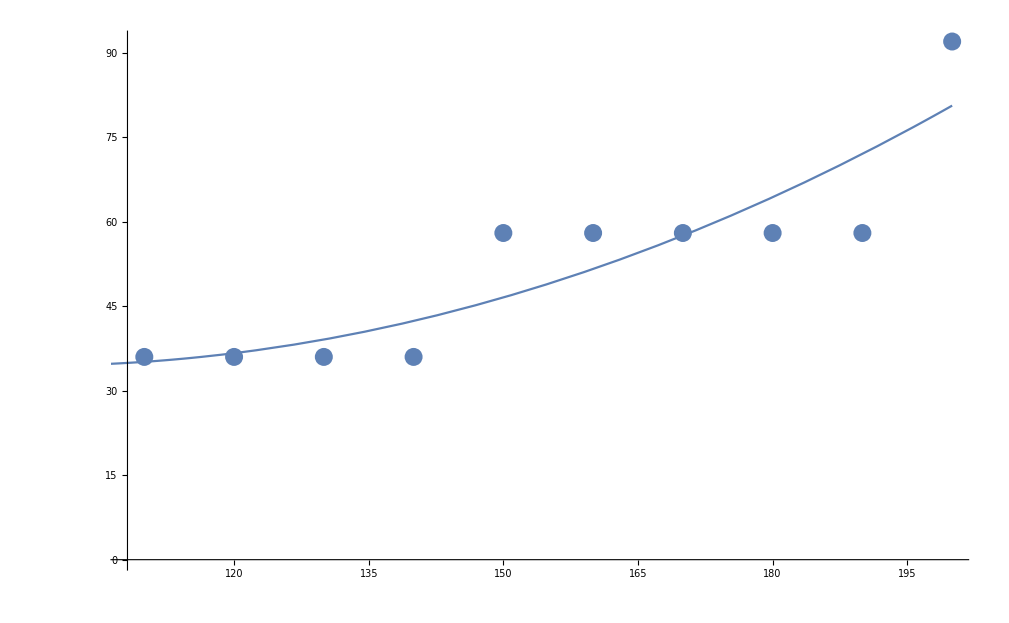

```mathematica
f1 = Fit[log3, {1,x},x]
f2 = Fit[log3, {1,x,x^2}, x]
f3 = Fit[log3, {1,x,x^2,x^3}, x]
Show[ListPlot[log3], Plot[{f2}, {x, 0, 200}]]
```